# The Su-Schrieffer–Heeger (SSH) model

A source to the theory behind the SSH model is in this web site  ---->  https://phyx.readthedocs.io/en/latest/TI/Lecture%20 notes/1.html

## 0.0- MaTex Package for LaTex Fonts

```mathematica
Needs["MaTeX`"]
```

## 1.0 - Hamiltonian

```mathematica
Clear[dx,dz,H,t,δt,k,Energy01];
```

```mathematica
dx[k_,t_,δt_]:=(t-δt)Sin[k];
dz[k_,t_,δt_]:=2.0δt+2.0(t-δt)(Sin[k/2])^2;
```

```mathematica
t=1.0;
```

```mathematica
H[k_,δt_]:=({{dz[k,t,δt], dx[k,t,δt]}, {dx[k,t,δt], -dz[k,t,δt]}});
```

```mathematica
Manipulate[Plot[ {Eigenvalues[H[k,δt]]},{k,-π,π},Axes->{True,None},AxesStyle->{Dashed,None},AxesOrigin->{0.0,0.0},BaseStyle->{FontFamily->"Times New Roman",FontSize->20},FrameLabel->(MaTeX[#,Magnification->2]&)/@{"k","E(k)"},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Large,PlotStyle->{{Blue,Thickness[Large]},{Red,Thickness[Large]}},PlotRange->All],{δt,-0.5,0.5,Appearance->"Open"}]
```

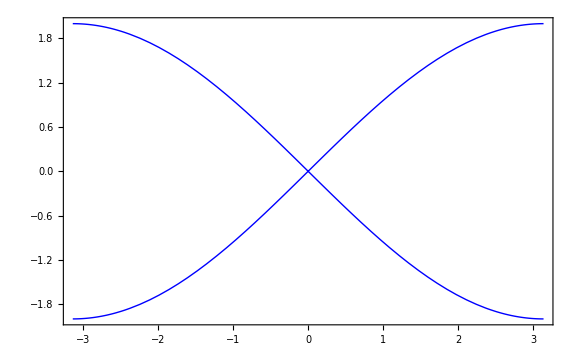

```mathematica
Energy01=Plot[ {Eigenvalues[H[k,0.0]]},{k,-π,π},Axes->{True,None},AxesStyle->{Dashed,None},AxesOrigin->{0.0,0.0},BaseStyle->{FontFamily->"Times New Roman",FontSize->22},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"k/\\pi","E(k)"},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Large,PlotStyle->{{Blue,Thickness[Large]},{Red,Thickness[Large]}},PlotLegends->Placed[(MaTeX[#,Magnification->3]&)/@{"\\delta t = 0.0"},{Scaled[{0,0.5}],{-1.70,-0.100}}],PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"Bulk_deltat_zero.pdf",Energy01,"PDF"]
```

/home/carlene/Dropbox/pós-doc-Utecht/Programas/SSH/SSH/Bulk_deltat_zero.pdf

## 2.0- Surface States with open boundary condition

### 2.1- Definition of the Hamiltonian with Open Boundary Conditions in the (01) Direction

```mathematica
Clear[matty,hstrip,Plotty,a,b,bT,aa,bb,cc];
```

```mathematica
matty[W_]:=Module[{hb},hb=ConstantArray[0,{W,W}];
For[i=1,i≤W,i++,
For[j=1,j≤W,j++,
If[i==j,hb[[i,j]]=a];
If[j-i==1,hb[[i,j]]=bT];
If[j-i==-1,hb[[i,j]]=b];]];hb];
matty[5]//MatrixForm
```

(a | bT | 0 | 0 | 0
b | a | bT | 0 | 0
0 | b | a | bT | 0
0 | 0 | b | a | bT
0 | 0 | 0 | b | a)

### 2.2- Definition of the Sub-Matrices “a” and “b”

```mathematica
Clear[W,kx,t,δt];
```

```mathematica
hstrip[W_,kx_,t_,δt_]:=Module[{},aa=({{δt+t, 0}, {0, -δt-t}});bb=({{-(t-δt)/2, ⅈ(t-δt)/2}, {ⅈ(t-δt)/2, (t-δt)/2}});
ArrayFlatten[matty[W]//. {a->aa,b->bb,bT->ConjugateTranspose[bb]}]];
```

```mathematica
$Assumptions=t∈Reals && δt∈ Reals;
```

```mathematica
hstrip[2,kx,t,δt]//MatrixForm
```

(t+δt | 0 | 1/2 (-Conjugate[t]+Conjugate[δt]) | -1/2 ⅈ (Conjugate[t]-Conjugate[δt])
0 | -t-δt | -1/2 ⅈ (Conjugate[t]-Conjugate[δt]) | 1/2 (Conjugate[t]-Conjugate[δt])
1/2 (-t+δt) | 1/2 ⅈ (t-δt) | t+δt | 0
1/2 ⅈ (t-δt) | (t-δt)/2 | 0 | -t-δt)

### 2.3- Plotting Module for the Eigenvalues of the Hamiltonian with Open Boundary Conditions

```mathematica
Clear[Lx,EigVals,hstore,k,Eig];
```

```mathematica
Plotty[Lx_,t_,δt_]:=Module[{EigVals,hstore,k},
hstore=hstrip[Lx,kx,t,δt];
EigVals=ConstantArray[0,Lx];For[i=1,i≤Lx,i++,k=-π+(2π(i-1))/(Lx);Eig=Sort[Eigenvalues[hstore/.{kx->k}]];EigVals[[i]]=Eig;];Show[{ListLinePlot[Transpose[EigVals],DataRange->{-π,π},PlotRange->All,Axes->True,AxesStyle->{{Dashed,Black},None},BaseStyle->{FontFamily-> "Times",FontSize->20}, PlotStyle->{{Darker[Blue]}},FrameLabel->(MaTeX[#,Magnification->2]&)/@{"k","E(k)"},AspectRatio->0.6,Frame->True,FrameTicksStyle->{{Black,Blue},{Black,Green}},FrameTicks->{Automatic,{{-π,0,π},None}}]},AxesOrigin->{-π,0},ImageSize->Large]];
```

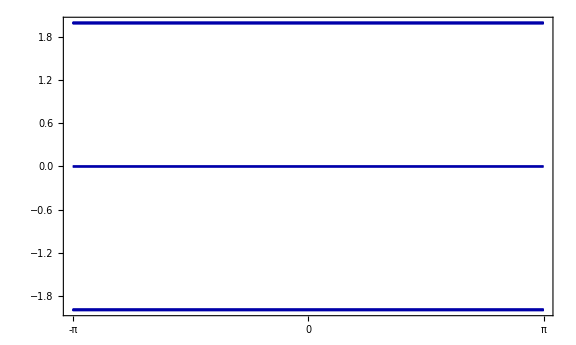

```mathematica
Plotty[10,1.0,-1.0]
```

```mathematica
Clear[PlotTrivialcase,PlotTopologicalcase]
```

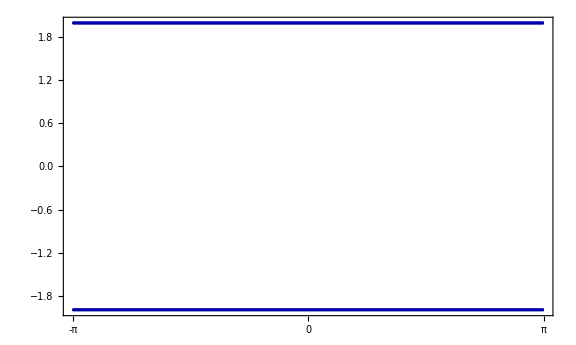

```mathematica
PlotTrivialcase=Plotty[10,1.0,1.0]
```

```mathematica
(*Export[NotebookDirectory[]<>"Edge_fully_dimerized_trivial.pdf",PlotTrivialcase,"PDF"]*)
```

```mathematica
PlotTopologicalcase=Plotty[10,1.0,-1.0]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"Edge_fully_dimerized_non-trivial.pdf",PlotTopologicalcase,"PDF"]*)
```